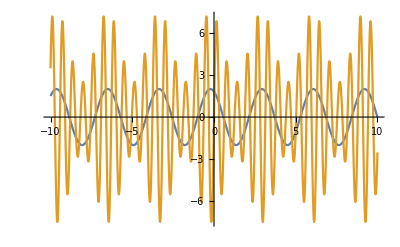

```mathematica
m=.5;

(* Carrier *)
Uc=5;ωc=10;
uc=Uc*Sin[ωc*#1]&;
(* Message *)
Um=2;ωm=2;ϕ=Um;
um=Um*Sin[ωm*#1+ϕ]&;

(* Amplitude Modulation *)
max=MaxValue[um[q],q];
uam=uc[#1]*(1+m*(um[#1])/(max))&;

Plot[{um[x],uam[x]},{x,-10,10}]
```

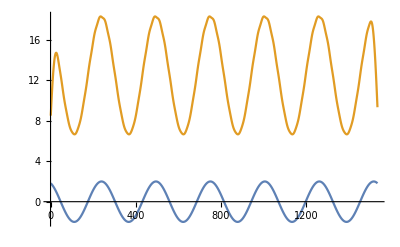

```mathematica
cardata=uc[Range[-3Pi,3Pi,Pi/256]];
src=um[Range[-3Pi,3Pi,Pi/256]];
data=uam[Range[-3Pi,3Pi,Pi/256]];
lowdata=LowpassFilter[data*cardata,2,SampleRate->50];
ListLinePlot[{src,lowdata}]
(*ListLinePlot[{src,lowdata-12.5}]*)
(*Periodogram[#,PlotRange->{{0,.1},{-40,40}},ImageSize->Large]&/@{src,data,lowdata2}*)
```